## Lab 3: Performance modelling

Students: August Heltne-Karlson and Erik Turøy Midtun

### Task 1: Analytic solution of small birth-death Markov chain using Mathematica (Warm up) [0%]

The example in this section demonstrates how to : 
1) Set up the equations that are needed to obtain the steady state probabilities 
2) Determine performance measures from the steady state probabilities (e.g., utilization, loss, expected number) 
A few useful functions and tricks are included.

Task : Run through the example step by step.

The example is a two server system with no queue (M/M/2/2).


-Graphics-

Define the state variables - put them in a table

```mathematica
vars = {Subscript[p, 0],Subscript[p, 1],Subscript[p, 2]}; (* shift + ctrl gives subscript *)
```

Set of equations

```mathematica
eqn = {
λ Subscript[p, 0] == μ Subscript[p, 1],
λ Subscript[p, 1] == 2μ Subscript[p, 2],
Subscript[p, 0]+Subscript[p, 1]+Subscript[p, 2]==1} (* = and = gives == *)
```

{λ p_0==μ p_1,λ p_1==2 μ p_2,p_0+p_1+p_2==1}

Analytic solution

```mathematica
sol=Solve[eqn,vars] // Flatten (* Flatten to reduce the levels of nested vector/sets - just try with and without *)
```

{p_0→(2 μ^2)/(λ^2+2 λ μ+2 μ^2),p_1→(2 λ μ)/(λ^2+2 λ μ+2 μ^2),p_2→λ^2/(λ^2+2 λ μ+2 μ^2)}

Define a set of parameter values to obtain the numerical solution

```mathematica
para = {λ-> 0.9,μ-> 1.0} (* - followed by > gives -> *)
```

{λ→0.9,μ→1.}

Numerical solution : /. means apply rule ("para" in this case) to the set/vector "sol"

```mathematica
nsol = sol /. para (* try with different parameters in "para" *)
```

{p_0→0.433839,p_1→0.390456,p_2→0.175705}

Obtain performance measures
- Utilisation (util) is equal to probability that server is non - empty
- Loss (loss) is the probability that all (both) resources are taken (time congestion)

```mathematica
util = 1-Subscript[p, 0] 
loss = Subscript[p, 2]
```

1-p_0

p_2

- Expected number of servers in used (exp) - calculated in five different ways

```mathematica
exp = 0 Subscript[p, 0] + 1 Subscript[p, 1] + 2 Subscript[p, 2] 
exp = Sum[i Subscript[p, i],{i,0,2}]
exp = ∑_{i,0,2} i Subscript[p, i]
exp = {0,1,2} . vars 
exp = Range[0,2] . vars
```

p_1+2 p_2

p_1+2 p_2

p_1+2 p_2

«2 more identical outputs»

Use of Map (/@)  function

```mathematica
(* Make a set of numbers from 0 to 2 *)
Range[0,2]
(* Make a set of 1 *)
Table[1,{3}]
(* Make a set of Subscript[p, i] for i=0,1,2 *)
Subscript[p, #] & /@ Range[0,2] 
(* Summarise all elements in a set by vector multiplication *)
(Subscript[p, #] & /@ Range[0,2]) . Table[1,{3}]
(* Expected value "exp" again *) 
(# Subscript[p, #] & /@ Range[0,2]) . Table[1,{3}]
```

{0,1,2}

{1,1,1}

{p_0,p_1,p_2}

p_0+p_1+p_2

p_1+2 p_2

Substitute the p_i’s in util, loss, and exp with the solution from sol  and nsol

```mathematica
(* Apply rule, "sol" to obtain the symbolic experession *)
aexp = exp /. sol
(* Simplify *)
aexp = exp /. sol//Simplify
aloss = loss /. sol//Simplify
autil = util /. sol //Simplify
(* Apply rule, "nsol" to obtain the numerical experession *)
nexp = exp /. nsol
nloss = loss /. nsol
nutil = util /. nsol
```

(2 λ^2)/(λ^2+2 λ μ+2 μ^2)+(2 λ μ)/(λ^2+2 λ μ+2 μ^2)

(2 λ (λ+μ))/(λ^2+2 λ μ+2 μ^2)

λ^2/(λ^2+2 λ μ+2 μ^2)

(λ (λ+2 μ))/(λ^2+2 λ μ+2 μ^2)

0.741866

0.175705

0.566161

Define a function
i) Example : CDF of NegExp
ii) Function to obtain loss, utilisation and expected values when the set of state probabilities is known.
a = arrival intensity, b = server rate
set = 
i)  {0,0,1} : loss
ii) {0,1,1} : util
iii){0,1,2} : exp

```mathematica
(* CDF of negative exponential distribution with intensity λ *)
F[t_] := 1 - Exp[-λ t]
```

1-ⅇ^(-t λ)

1-ⅇ^-t

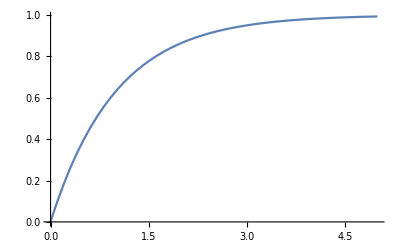

Piecewise[{{1-ⅇ^(-t λ), t≥0}, {0, True}}]

```mathematica
F[t]
F[t] /. {λ->1}
Plot[F[t] /. {λ->1}, {t,0,5}]
(* NOTE: this function already exists in Mathematica *) 
CDF[ExponentialDistribution[λ],t]
```

```mathematica
(* Function to obtain loss, utilisation and expected values (the "set" is different depending on what you are going to calculate) when the set of state probabilities is known. *) 
AGen[a_,b_,set_] := set . vars /. (sol /. {λ->a,μ->b})
```

Plot : utilisation (set={0,1,1}) and loss (set={0,0,1}) for different values of λ with μ = 1

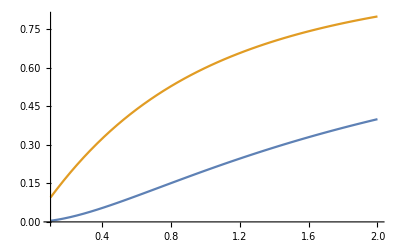

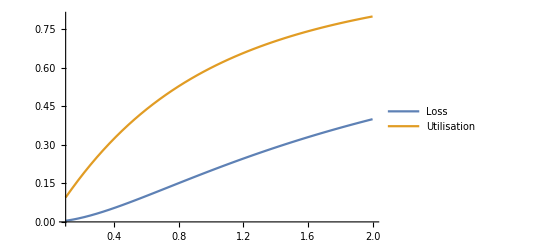

```mathematica
Plot[{AGen[λ,1,{0,0,1}],AGen[λ,1,{0,1,1}]},{λ,0.1,2}]
(* Think about why, for instance set={0,1,1} will give us the utilisation *)
Plot[{Legended[AGen[λ,1,{0,0,1}],"Loss"],Legended[AGen[λ,1,{0,1,1}],"Utilisation"]},{λ,0.1,2}]
```

### Task 2: Runways [25%]

Let the system state be the number of airplanes in landing and in the airspace over the airport. 
NOTE: Takeoffs are not included in this part of the assignment.
The airspace has a limited capacity. Arriving airplanes will be redirected if both runways are in use and the airspace is full. 
	2.1. Draw the Markov chain model for two runways (n=2) and N=10.  What kind of queue model is this in Kendall’s notation?
	 -Graphics-
	M/M/2/10/FIFO queue model

2.2. Set up the equations and solve them to determine the steady state probabilities for n=2 and N=10.

```mathematica
vars = Subscript[p, #] & /@ Range[0,10]
```

{p_0,p_1,p_2,p_3,p_4,p_5,p_6,p_7,p_8,p_9,p_10}

```mathematica
eqns = {
λ Subscript[p, 0] == μ Subscript[p, 1],
λ Subscript[p, 1] == 2μ Subscript[p, 2],
λ Subscript[p, 2] == 2μ Subscript[p, 3],
λ Subscript[p, 3] == 2μ Subscript[p, 4],
λ Subscript[p, 4] == 2μ Subscript[p, 5],
λ Subscript[p, 5] == 2μ Subscript[p, 6],
λ Subscript[p, 6] == 2μ Subscript[p, 7],
λ Subscript[p, 7] == 2μ Subscript[p, 8],
λ Subscript[p, 8] == 2μ Subscript[p, 9],
λ Subscript[p, 9] == 2μ Subscript[p, 10],
vars . Table[1,{11}]==1
};
sol=Solve[eqns,vars] //Flatten
```

{p_0→(512 μ^10)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_1→(512 λ μ^9)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_2→(256 λ^2 μ^8)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_3→(128 λ^3 μ^7)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_4→(64 λ^4 μ^6)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_5→(32 λ^5 μ^5)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_6→(16 λ^6 μ^4)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_7→(8 λ^7 μ^3)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_8→(4 λ^8 μ^2)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_9→(2 λ^9 μ)/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10),p_10→λ^10/(λ^10+2 λ^9 μ+4 λ^8 μ^2+8 λ^7 μ^3+16 λ^6 μ^4+32 λ^5 μ^5+64 λ^4 μ^6+128 λ^3 μ^7+256 λ^2 μ^8+512 λ μ^9+512 μ^10)}

2.3. Solve the equations and obtain the expected number of runways in use and the expected number of planes in the airspace,as a function of λ {plot for λ∈[0.5, 5]} with μ=1.

Explain how and why the utilisation flattens out, and and argue for what you regard as an acceptable arrival rate λ.

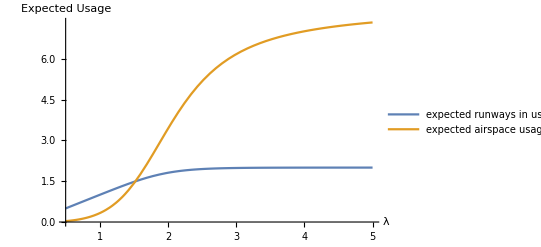

```mathematica
para={n->2,N->10};
(*expRunways=∑{i,0,N}Min[i,n]*pi/.para*)
expRunwaysMask={0,1,2,2,2,2,2,2,2,2,2};
expAirspaceMask={0,0,0,1,2,3,4,5,6,7,8};
Plot[{Legended[AGen[λ,1,expRunwaysMask],"expected runways in use"],Legended[AGen[λ,1,expAirspaceMask],"expected airspace usage"]},{λ,0.5,5}, AxesLabel->{λ, "Expected Usage"}]
```

The utilisation of the runways and the airspace flatten out because they fill up. The runways have a capacity of maximum 2 planes handled at the same time because each runway can handle one plane at a time. The expected value of runways flattens out when it reaches two because the moment a planes leaves the runway, a new plane from the airspace enters the runway. Based on the graph above, a lambda value between 2 and 3 would give acceptable waiting times for the runway without wasting resources. The most important thing to note is that a lambda value of around 5 will result in a full airspace and force the airport to reject planes. This should be avoided.

2.4. Plot the probability of redirected airplanes (n=2, N=10) as a function of λ ∈[0.5, 5] (with μ=1). 		
		Argue for what you regard as an acceptable arrival rate λ.

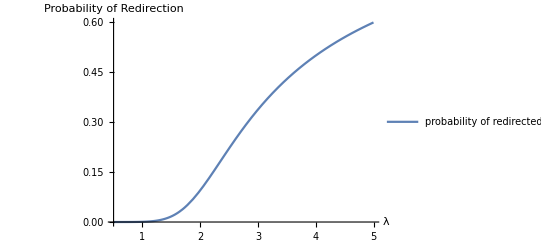

```mathematica
lossMask = {0,0,0,0,0,0,0,0,0,0,1};
Plot[{Legended[AGen[λ,1,lossMask],"probability of redirected planes"]},{λ,0.5,5},AxesLabel->{λ, "Probability of Redirection"}]
```

Given that rejecting an airplane is really bad for the passengers, the probability of being redirected should be as close to zero as possible. Therefore we suggest that an arrival rate between 1 and 1.25 should be chosen. While this comes at a cost to the total amount of planes that arrives per day, most passengers value dependability highly and would rather have fewer flights to choose between instead of being forced to land in another city.

2.5. Make a function in Mathematica which implements Erlang's C formula (E_(2,n)(A) in Eq.(6.95) in the textbook). 
	Check that it returns E_(2,2)(A)=A^2/(2+A) (n=2 and where A=λ/μ).
	The probability of waiting  in a M/M/n -queue is given by Erlang’s C formula.

```mathematica
ErlC[A_,n_] := (((A^n)/n!)*n/(n-A))/(∑_{i,0,n-1} ((A^i)/i!)+(((A^n)/n!)*n/(n-A)))
```

```mathematica
para3 ={A->λ /μ };
erlangCTest = ErlC[A, 2] //Simplify
```

A^2/(2+A)

2.6. Use the appropriate formulas from Chapter 6 to obtain the expected (sojourn) time E[S] in the system when n=2 and N is infinite.
From Eq.(6.100) in the book we get the following function:

```mathematica
ExpSoujourn[A_,n_,μ_] := (1/((n-A)*μ))*(ErlC[A,n]+n-A)
```

2.7. Plot the probability that both runways are free as a function of λ ∈[1,3] (with μ=1) with N=10 and N infinite. (Comment results).

The probability that both runways are free is the same as p_0.

```mathematica
SteadyStateForMMn[A_,n_,i_] := If[i<n,((A^i)/i!)/(∑_{j,0,n-1} ((A^j)/j!)+(((A^n)/n!)*(n/(n-A)))) ,((A^i)/n!n^(i-n))/(∑_{j,0,n-1} ((A^j)/j!)+(((A^n)/n!)*(n/(n-A))))]
```

(2-λ)/(2+λ)

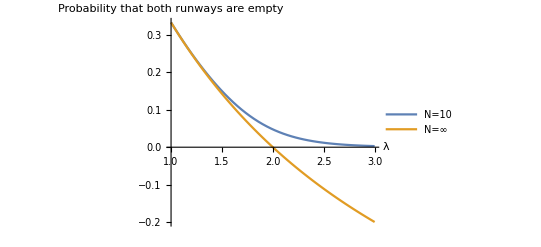

```mathematica
p0mmnNinf = SteadyStateForMMn[A,2,0] /. {A->λ /1 } //Simplify
emptyMaskN10 = {1,0,0,0,0,0,0,0,0,0,0};
Plot[{Legended[AGen[λ,1,emptyMaskN10],"N=10"], Legended[p0mmnNinf,"N=∞"]},{λ,1,3},AxesLabel->{λ, "Probability that both runways are empty"}]
```

With a finite queue there’s always the possibility that all planes in the airspace get to land before another plane arrives. This can be seen in the N = 10 graph where the probability is very low, but non-zero. For N = ∞, the probability of both runways being free is 0 at λ = 2 and becomes negative afterwards. This is caused by the system being unstable. For M/M/2, the following condition must be met for the system to be stable: 2 > λ/μ. With μ = 1 and λ >= 2, this condition is not met and the queue will approach ∞.

### Task 3: Deicing station [20%]

The objective in this task is to check the effect of changing the number of deicing stations, n. Assume infinite queuing capacity. 
3.1. Draw the Markov chain model for n deicing stations. What kind of queue model is this in Kendall’s notation?
	-Graphics-
	M/M/n/∞/FIFO

3.2. Set up the equations and solve them to provide the steady state probabilities for n=1.

```mathematica
vars = Subscript[p, #] & /@ Range[0,10];
eqns3an = {
λ Subscript[p, 0] == μ Subscript[p, 1],
λ Subscript[p, 1] == Min[2, n]μ Subscript[p, 2],
λ Subscript[p, 2] == Min[3, n]μ Subscript[p, 3],
λ Subscript[p, 3] == Min[4, n]μ Subscript[p, 4],
λ Subscript[p, 4] == Min[5, n]μ Subscript[p, 5],
λ Subscript[p, 5] == Min[6, n]μ Subscript[p, 6],
λ Subscript[p, 6] == Min[7, n]μ Subscript[p, 7],
λ Subscript[p, 7] == Min[8, n]μ Subscript[p, 8],
λ Subscript[p, 8] == Min[9, n]μ Subscript[p, 9],
λ Subscript[p, 9] == Min[10, n]μ Subscript[p, 10],
vars . Table[1,{11}]==1
};
sol1=Solve[eqns3an /. {n-> 1},vars] //Flatten
```

{p_0→μ^10/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_1→(λ μ^9)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_2→(λ^2 μ^8)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_3→(λ^3 μ^7)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_4→(λ^4 μ^6)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_5→(λ^5 μ^5)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_6→(λ^6 μ^4)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_7→(λ^7 μ^3)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_8→(λ^8 μ^2)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_9→(λ^9 μ)/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10),p_10→λ^10/(λ^10+λ^9 μ+λ^8 μ^2+λ^7 μ^3+λ^6 μ^4+λ^5 μ^5+λ^4 μ^6+λ^3 μ^7+λ^2 μ^8+λ μ^9+μ^10)}

3.3. Use the functions from Queueing Processes to obtain the steady state probabilities for n=1 and n=2.
	Plot (use ListPlot) the steady state probabilities of states 0-10 for n=1 and n=2. (λ=0.07,μ=0.1). Compare and comment the difference between n=1 and n=2.

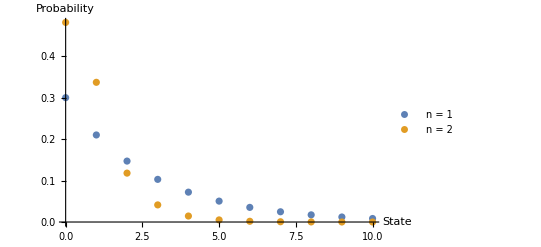

```mathematica
𝒫= {λ-> 0.07,μ->0.1}; 
(*QueueProperties[𝒬] //Simplify; *)
Subscript[𝒟, 1] = StationaryDistribution[QueueingProcess[λ,μ,1,Infinity]];
Subscript[𝒟, 2] = StationaryDistribution[QueueingProcess[λ,μ,2,Infinity]];
(* Numerical probablities of all states_*)
steadyStateN1 =Probability[n== #, n\[Distributed] Subscript[𝒟, 1]]& /@ Range[0,10] /. 𝒫;
steadyStateN2 =Probability[n== #, n\[Distributed] Subscript[𝒟, 2]]& /@ Range[0,10] /. 𝒫;
ListPlot[{Legended[steadyStateN1, "n = 1"], Legended[steadyStateN2, "n = 2"]}, DataRange->{0,10}, AxesLabel->{"State", "Probability"}]
```

We can see that the probability having a large queue decreases faster for n = 2 than for n = 1. This is due to the fact that for n = 2, airplanes leave the system with a rate of 2μ compared to n = 1 where the rate is μ. As such n = 2 has a higher probability of being in a state with few airplanes in the queue and a lower probability of being in a state with a lot of airplanes in the queue.

3.4. Use the functions from Queueing Processes to obtain a symbolic expression the time at deicing, E[S] for n.

```mathematica
𝒬 =QueueingProcess[λ,μ,n,Infinity];
QueueProperties[𝒬] //Simplify;
QueueProperties[𝒬,"MeanSystemTime"] //Simplify
```

1/μ+(n (λ/μ)^n μ Gamma[n])/((-λ+n μ) (n (λ/μ)^n μ Gamma[n]-ⅇ^(λ/μ) (λ-n μ) n! Gamma[n,λ/μ]))

3.5. Plot the E[S] for n=1,..,10 (deicing stations), using the following parameters : {λ=0.1, μ=0.1}. How does the E[S] change with n?  How many  deicing stations would you recommend (argue)?

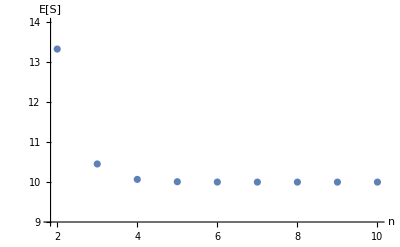

```mathematica
𝒫= {λ-> 0.1,μ->0.1};
𝒬 =QueueingProcess[λ,μ,n,Infinity];
queue =QueueProperties[𝒬,"MeanSystemTime"] /. 𝒫//Simplify ;
probs1 =Table[{n,queue},{n,2,10}];
ListPlot[{probs1}, DataRange->{2,10}, PlotRange->{9,14}, AxesLabel->{"n", "E[S]"}]
```

If the system only has a single deicing truck the condition 1 > A is not met and the system is therefore not stable. The result for a single truck is therefore omitted from the graph. Based on the graph above, one would either pick three or four deicing trucks as those yield the highest return on investment. Five deicing trucks are barely better than four trucks and the expected time for two trucks is much higher than the expected time for three trucks.

### Task 4: Turnaround at gate [15%]

After landing, the airplane is taxing to the gate where unloading and reloading take place, before the plane leaves the gate and is ready for takeoff.  The the expected turnaround time is 1/μ_t.  There is always a gate available for an arriving airplane.
4.1. Suggest a queueing model for the gates (you may use Kendall’s notation)
M/M/∞/∞/FIFO

4.2. Obtain (on paper if you like) a symbolic expression for the steady state probabilities. What is this probability distribution called?
-Graphics-

4.3. Use the "QueueingProcess" to obtain the same steady state probabilities.

```mathematica
𝒬 =QueueingProcess[λ,μ,Infinity,Infinity];
QueueProperties[𝒬]//Simplify ;
𝒟 =StationaryDistribution[𝒬];
Probability[ n== i,n\[Distributed]𝒟]
```

Piecewise[{{(ⅇ^(-λ/μ) (λ/μ)^i)/(i!), i==Floor[i]&&i≥0}, {0, True}}]

We can see that this expression is the same as the one we found in 4.2 with A substituted by λ/μ. 
 
4.4. Plot the probability that n=0, 1, 2, 3, 4 gates are occupied. 
	(para = {λ→0.9,μ_t→1})

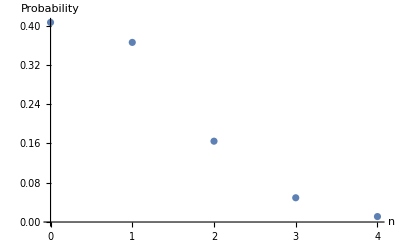

```mathematica
𝒫= {λ->0.9,Subscript[μ, t]->1};
𝒬 =QueueingProcess[λ,Subscript[μ, t],Infinity,Infinity];
𝒟 =StationaryDistribution[𝒬];
Subscript[p, x_] := PDF[𝒟,x];
probs= Subscript[p, #]&/@Range[0,4] /. 𝒫;
ListPlot[{probs}, DataRange->{0,4}, AxesLabel->{"n", "Probability"}]
```

4.5. Obtain the E[W] (time in the system). Compare with the expected service time (1/μ_t) and comment on the result.

```mathematica
QueueProperties[𝒬, "MeanSystemTime"]//Simplify
```

1/μ_t

As the system has infinite capacity no time will be spent waiting for the service and there is no queueing to leave the system. As such E[W] is equal to E[S].

### Task 5: The airport in cold weather [40%]

In this task it is expected that you solve the problem without help from the assistants (only to clarify any ambiguities and typos) - you’re on your own... 

In our system (the airport), an airplane needs 
	- access to a runway twice (landing and takeoff), 
	- a gate for turnaround of passengers and goods, 
	- and in case of cold weather it also needs a deicing station.  
In this task you should assume that there is cold weather (but no snow). The runways are shared between landing and takeoff and in this analytic model we assume no priority between the two.

Model the total “life cycle” of an airplane a network of queues using the Jackson’s theorem 
[[Mathematica has a “QueueingNetworkProcess” which is useful]].
5.1. Explain how to apply the Jackson’s theorem and list the assumptions
The main application of the Jackson ‘s theorem is that it allows us to create a network of nodes and still study the individual nodes independently after we have determined A_k for all the nodes.

Conditions needed for Jackson’s Theorem:
	1. Customers arrive from outside the system at node k according to a Poisson process with intensity λ_k.
	2. The number of servers in node k is n_k >= 1 where k = 1, ... , K. The service time in node k is negative 			exponentially distributed with parameter μ_k. 

These conditions are both fulfilled as all the nodes are M/M/n with n >= 1.

	3. Each node has an infinite number of queueing positions.

We can fulfill this condition by modelling all the queues as M/M/n/∞.

	4. After a service completion at node k a customer is either instantaneously routed to and received at node j 	with probability p_kj, or leaves instantaneously the system with probability p_k0 = 1 - ∑_(j=1)^K p_kj.

This condition is fulfilled as all customers leaving the runway the first time are instantly sent to the gate. After finishing at the gate the customer is instantly sent to the deicing station and after finishing at the deicing station the plane returns to the runway. When leaving the runway the second time, the customer leaves the system instantly. 

5.2. What are the “customers” and “nodes” in the system?

The nodes are the runways, the deicing stations and the gates.
The customers are the planes as they are requesting service from the nodes.

5.3. Suggest a queue model type (M/M/?) for each node (the nodes might need different kinds of queue model)?

Runways: M/M/2/∞/FIFO
	We use the same variables for runways as in Task 2 with the queue capacity increased to ∞ due to condition 3.

Deicing Stations: M/M/2/∞/FIFO
	Due to us observing that the deicing stations required n > 1 to be stable, we use two deicing stations.
	
Gates: M/M/∞/∞/FIFO
	Gates keep the same variables from Task 4.

5.4. Draw the model (show the network of queues and indicate what type of queue you have in each node)

-Graphics-

5.5. Define the total arrival intensity for each of the queues (nodes) in the network of queues

```mathematica
vars = {Subscript[Λ, 1], Subscript[Λ, 2], Subscript[Λ, 3]};
eqns = {
Subscript[Λ, 1]== Subscript[λ, 1]+Subscript[Λ, 3],
Subscript[Λ, 2] == Subscript[λ, 2]+Subscript[p, 12] Subscript[Λ, 1],
Subscript[Λ, 3]==  Subscript[λ, 3]+Subscript[Λ, 2]
};
sol=Solve[eqns,vars] ;
para5 ={Subscript[λ, 1]-> 1, Subscript[λ, 2]-> 0, Subscript[λ, 3] -> 0, Subscript[p, 12] -> 0.5, μ -> 0};
nsol3 = sol /. para5
```

{{Λ_1→2.,Λ_2→1.,Λ_3→1.}}

The cell above is quite unstable due to other functions. The proper output is {Λ_1→2.,Λ_2→1.,Λ_3→1.}.

5.6. Apply "QueueingNetworkProcess" to specify the network model

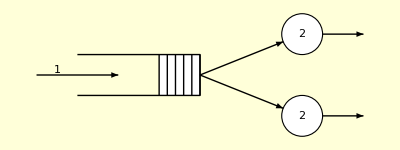
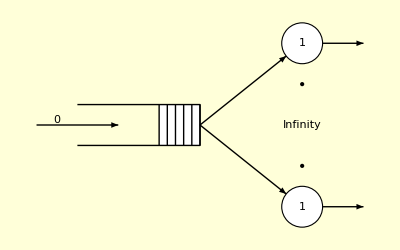
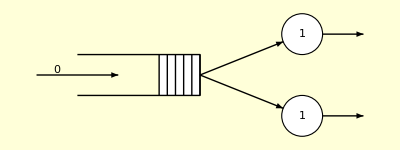
{-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 3
SelectedNode | 1
Performance Measures | 
MeanSystemSize | 1.33333
MeanSystemTime | 0.666667
MeanQueueSize | 0.333333
MeanQueueTime | 0.166667,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 3
SelectedNode | 2
Performance Measures | 
MeanSystemSize | 1.
MeanSystemTime | 1.
MeanQueueSize | 0.
MeanQueueTime | 0.,-Graphics- | 
Basic Properties | 
NetworkType | Open
NodeCount | 3
SelectedNode | 3
Performance Measures | 
MeanSystemSize | 1.33333
MeanSystemTime | 1.33333
MeanQueueSize | 0.333333
MeanQueueTime | 0.333333}

```mathematica
γ={1,0,0};
μ={2,1,1};
r={{0,0.5,0},{0,0,1},{1,0,0}};
c={2,Infinity,2};

𝒩=QueueingNetworkProcess[γ,r,μ,c];
Table[QueueProperties[{𝒩,i}],{i,3}]
node1 = QueueingProcess[2,2,2];
node2 = QueueingProcess[1,1,Infinity];
node3 =QueueingProcess[1,1,2];
```

5.7. What is the probability that both runways are idle?

```mathematica
network=QueueingNetworkProcess[γ,r,μ,c];
distribution=StationaryDistribution[network];
Total[Total[Table[PDF[distribution,{0,i,k}],{i,0,20},{k,0,20}]]]
PDF[StationaryDistribution[node1],0]
```

0.333333

1/3

As the network is a Jackson network, we can examine the nodes independently or a part of the system. As shown above, both of these methods will lead to the same answer. This property is also used for the following two questions.

	What is the probability that there are 4 airplanes?

```mathematica
combos = Select[Tuples[Range[0,4],3],Total@#≤4&];
subs =Select[combos,Total[#]== 4&];
probs = Table[PDF[distribution,sub],{sub,subs}];
Grid[{subs,probs}]
Total[probs]
```

{0,0,4} | {0,1,3} | {0,2,2} | {0,3,1} | {0,4,0} | {1,0,3} | {1,1,2} | {1,2,1} | {1,3,0} | {2,0,2} | {2,1,1} | {2,2,0} | {3,0,1} | {3,1,0} | {4,0,0}
0.00510944 | 0.0102189 | 0.0102189 | 0.00681258 | 0.00170315 | 0.0102189 | 0.0204377 | 0.0204377 | 0.00681258 | 0.0102189 | 0.0204377 | 0.0102189 | 0.0102189 | 0.0102189 | 0.00510944

0.158393

We assume that the question is “What is the probability that there are 4 airplanes in the system at the same time?”. To solve this, we calculate the sum of the probability of each permutation of airplanes in the system that has a sum of 4. This cell has a tendency to give out unreadable output, but the total output is:
-Graphics-
	What is the probability that one airplane is at the deicing station?

```mathematica
distribution=StationaryDistribution[node3];
PDF[distribution, 1]
```

1/3

5.8. Obtain an expression for the expected number of airplanes in at the airport

```mathematica
γ={λ,0,0};
μ={2,1,1};
r={{0,0.5,0},{0,0,1},{1,0,0}};
c={2,Infinity,2};
𝒩 = QueueingNetworkProcess[γ,r,μ,c];
Total[Table[QueueProperties[{𝒩,i}, "MeanSystemSize"],{i,3}]] // Simplify
```

3. λ+(λ^3 (-1./(1. λ^2+ⅇ^(1. λ) (2.-1. λ) Gamma[2,1. λ])-1./(1. λ^2+ⅇ^(1. λ) (2.-1. λ) Gamma[2,0.+1. λ])))/(-2.+1. λ)

5.9. Obtain an expression for the expected time at the airport, E[S_a].

```mathematica
γ={λ,0,0};
μ={2,1,1};
r={{0,0.5,0},{0,0,1},{1,0,0}};
c={Subscript[N, run],Infinity,Subscript[N, ice]};
𝒩 = QueueingNetworkProcess[γ,r,μ,c];
expectedTimeAtAirport = Total[Table[QueueProperties[{𝒩,i}, "MeanSystemTime"],{i,3}]] // Simplify
```

2.5+(1. λ^N_ice)/(N_ice! ((ⅇ^(1. λ) Gamma[N_ice,0.+1. λ])/Gamma[N_ice]+(1. λ^N_ice)/(N_ice!-(1. λ N_ice!)/N_ice)) (1-(1. λ)/N_ice)^2 N_ice)+(0.5 λ^N_run)/(N_run! ((ⅇ^(1. λ) Gamma[N_run,0.+1. λ])/Gamma[N_run]+(1. λ^N_run)/(N_run!-(1. λ N_run!)/N_run)) (1-(1. λ)/N_run)^2 N_run)

5.10. Plot the expected time at the airport for different λ values.  
	Argue for what you regard as an acceptable arrival rate λ wrt. to total time at airport for an airplane.

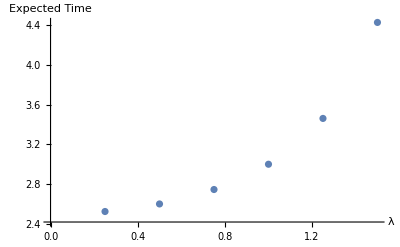

0.25 | 0.5 | 0.75 | 1 | 1.25 | 1.5
2.52381 | 2.6 | 2.74545 | 3. | 3.46154 | 4.42857

```mathematica
expectedTimeAtAirportWithParam = expectedTimeAtAirport /. {Subscript[N, run] -> 2,Subscript[N, ice] ->2};
ListPlot[Table[expectedTimeAtAirportWithParam,{λ,{0.25,0.5,0.75,1,1.25,1.5}}], DataRange->{0.25,1.5}, AxesLabel->{λ, "Expected Time"}]
Grid[{{0.25,0.5,0.75,1,1.25,1.5},
Table[expectedTimeAtAirportWithParam,{λ,{0.25,0.5,0.75,1,1.25,1.5}}]}]
```

With the variables used for this network we can see that the expectedTimeAtAirport rises exponentially with λ. When λ reaches 2, the system will become unstable and the expected time will approach ∞.

In order to maximize performance we want to pick a λ such that λ is high and the expected time is low. This can be done by calculating and comparing values for λ/E[S]:
-Graphics-
Based on this, picking λ = 1.25 would be the best choice for optimizing performance. The truly optimal λ can be found by analyzing the function, but we regard this as out of scope and it will only result in minor gains.


5.11 Investigate where the bottleneck is and discuss which changes can be made (in service rates, resource capacities) if the arrival intensity λ is fixed and the total time at the airport  E[S_a] is regarded as too high.

There are two ways we can reduce the total time at the airport:
	1. Reduce time spent in queues by increasing capacity
	2. Reduce time spent in service by reducing service time. This will also reduce time spent in queues, but is 		harder to do in a real life scenario.

```mathematica
γ={λ,0,0};
μ={2,1,1};
r={{0,0.5,0},{0,0,1},{1,0,0}};
c={Subscript[N, run],Infinity,Subscript[N, ice]};
𝒩 = QueueingNetworkProcess[γ,r,μ,c];
expectedTimeAtAirport = Total[Table[QueueProperties[{𝒩,i}, "MeanSystemTime"],{i,3}]] // Simplify;
Print["Increasing the number of deicing stations"]
Table[expectedTimeAtAirport /. {λ -> 1.25,Subscript[N, run] -> 2,Subscript[N, ice] ->i},{i,2,10}]
Print["Increasing the number of runways"]
Table[expectedTimeAtAirport /. {λ -> 1.25,Subscript[N, run] -> i,Subscript[N, ice] ->2},{i,2,10}]
```

Increasing the number of deicing stations

{3.46154,2.90935,2.83586,2.8231,2.82092,2.82057,2.82052,2.82051,2.82051}

Increasing the number of runways

{3.46154,3.18545,3.1487,3.14232,3.14123,3.14105,3.14103,3.14103,3.14103}

Increasing Capacity:
For the number of deicing stations, we get the same result as in Task 3.5 with the increase flattening out after 4 deicing stations. 
Increasing the amount of runways has a lesser effect compared to increasing the number of deicing stations, but going up to three runways is still a decent way to save time compared to two runways.
Increasing capacity is irrelevant for gates as we assume infinite capacity.

```mathematica
γ={λ,0,0};
μ={Subscript[u, runway],Subscript[u, gate],Subscript[u, deicing]};
r={{0,0.5,0},{0,0,1},{1,0,0}};
c={2,Infinity,2};
𝒩 = QueueingNetworkProcess[γ,r,μ,c];
expectedTimeAtAirport = Total[Table[QueueProperties[{𝒩,i}, "MeanSystemTime"],{i,3}]] // Simplify;
Print["Decreasing time for deicing"]
Table[expectedTimeAtAirport /. {λ -> 1.25,Subscript[u, runway] -> 2,Subscript[u, gate]-> 1, Subscript[u, deicing]->i},{i,1,10}]
Print["Decreasing time for landing / takeoff"]
Table[expectedTimeAtAirport /. {λ -> 1.25,Subscript[u, runway] -> i,Subscript[u, gate]-> 1, Subscript[u, deicing]->1},{i,2,10}]
Print["Decreasing time for turn around"]
Table[expectedTimeAtAirport /. {λ -> 1.25,Subscript[u, runway] -> 2,Subscript[u, gate]-> i, Subscript[u, deicing]->1},{i,1,10}]
```

Decreasing time for deicing

{3.46154,2.37463,2.16897,2.07677,2.02369,1.98901,1.96452,1.94628,1.93216,1.9209}

Decreasing time for landing / takeoff

{3.46154,3.04439,2.91808,2.85436,2.81525,2.78859,2.76915,2.75432,2.74261}

Decreasing time for turn around

{3.46154,2.96154,2.79487,2.71154,2.66154,2.62821,2.6044,2.58654,2.57265,2.56154}

Reducing service time:

Increasing μ_deicing from 1 to 2 gives an incredible increase to performance. This is partly due to the fact that we are halving the time needed to deice, but as the performance gains flatten out when you focus on a variable, reducing time for deicing is a good way to boost performance.

Both the runways and the gate show less effect than deicing, but are still worthwhile to optimize if possible. However, both of these are hard to optimize in a real life scenario. For example, halving the time needed to turn around a plane will be close to impossible as passengers require a large enough time window to board. Therefore one should rather be trying to either optimize deicing time or increase the amount of deicing stations and / or runways.

To conclude: 
The main bottleneck is the deicing stations and spending resources on either increasing capacity or reducing time needed to deice will yield good results. Do note the relationship between time needed to deice and capacity. Increasing the capacity and decreasing the time required to deice simultaneously will yield less returns than the numbers above might suggest. This is due to the fact that lowering the time per deice will also lower the probability that both of the deicing stations are in use when a new plane arrives. 
As decreasing “turn around”-time, landing-time and takeoff-time are hard in a real life scenario, increasing the amount of runways to three is the best choice for increasing performance outside of cold weather.

## Functions and hints

#### “Queueing Processes” from Mathematica

See : https://reference.wolfram.com/language/guide/QueueingProcesses.html  
Queueing Process Models
	QueueingProcess — represents a queue with general arrival and service distributions
	QueueingNetworkProcess — represents a network of connected queues
Performance Measures
	QueueProperties[data] — steady-state and other properties for queues
	ErlangB - Erlang-B loss formula
	ErlangC - Erlang-C delay formula

List content of function

```mathematica
?QueueingProcess
```

Example with M/M/2/4

```mathematica
QueueingProcess
```

QueueingProcess

```mathematica
𝒫= {λ-> 0.5,μ->1};
(* Example with M/M/2/4 *) 
𝒬 = QueueingProcess[λ,μ,2,4];
(* List all properties of M/M/2/4 *)
QueueProperties[𝒬] //Simplify;
(* List MeanSystemTime of M/M/2/4 *)
QueueProperties[𝒬,"MeanSystemTime"] //Simplify;
𝒟 = StationaryDistribution[𝒬];
Subscript[π, x_] := PDF[𝒟,x];
Subscript[π, #]&/@Range[0,4] (* same as writing {Subscript[π, 0],Subscript[π, 1],Subscript[π, 2],Subscript[π, 3]} - try it *) 
(* Numerical probablity of Subscript[π, 4]*)
Probability[n== 4, n\[Distributed]𝒟] /.𝒫;
(* Numerical probablities of all states_*)
Probability[n== #, n\[Distributed]𝒟]& /@ Range[0,4];
(* Loss in M/M/4/4 *)
ErlangB[4,λ/μ] /.𝒫;
ErlangC[2,λ/μ] /. 𝒫
```

{(8 μ^4)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),(8 λ μ^3)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),(4 λ^2 μ^2)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),(2 λ^3 μ)/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4),λ^4/(λ^4+2 λ^3 μ+4 λ^2 μ^2+8 λ μ^3+8 μ^4)}

0.1

#### Some editing hints

Mathematical Notation Characters
https://reference.wolfram.com/language/guide/MathematicalNotationCharacters.html 

Special Characters
https : // reference.wolfram.com/language/guide/SpecialCharacters.html

```mathematica
(* esc+<something>+esc *)
(* ex ...*)
(* λ esc+l+esc *)
(* ∑ esc+\sum+esc *)
(* 𝒟 esc+scD+esc *) 
(* 𝒬 esc+scQ+esc*)
```

shift + return = evaluate the cell
; at then end will not return the result

Help function: 
1) Use : ?+function, e.g., ?Plot
2) Mouseover gives you:  - both a dropdown menu ,  and an info-button that takes you directly to the help page.

```mathematica
?Plot
```

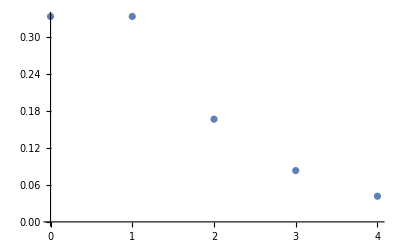

```mathematica
𝒫= {λ->2,Subscript[μ, t]->2};
𝒬 =QueueingProcess[λ,Subscript[μ, t],2,Infinity];
𝒟 =StationaryDistribution[𝒬];
Subscript[p, x_] := PDF[𝒟,x];
probs= Subscript[p, #]&/@Range[0,4] /. 𝒫;
ListPlot[{probs}, DataRange->{0,4}]
```